Вариант 8

{4.0585-19.365 X,True,4.57713}

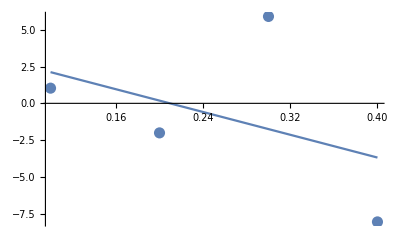

```mathematica
x={0.1,0.2,0.3,0.4};
y={1.032,-2.009,5.908,-8.062};
n=Length[x];
Tbl=Table[{x[[i]],y[[i]]},{i,1,n}];
eqv:=Table[∑_(i=0)^m Subscript[a, i]*∑_(j=1)^n (x[[j]])^(i+k)==∑_(j=1)^n y[[j]]*(x[[j]])^k,{k,0,m}];
Koef:=Solve[eqv,Table[Subscript[a, i],{i,0,m}]]//Flatten;
P[X_]:=(∑_(i=0)^m Subscript[a, i]*X^i)/.Koef
Ft[X_]:=Fit[Tbl,Table[X^i,{i,0,m}],X]
δ:=√(1/n*∑_(i=1)^n (y[[i]]-P[x[[i]]])^2)//N
Gr:=Show[ListPlot[Tbl,PlotStyle->{PointSize[0.02]}],Plot[P[X],{X,x[[1]],x[[n]]}]]
m=1;{P[X],((P[X]-Ft[X])//Chop)==0,δ}
Gr
```

{-9.60275+117.247 X-273.225 X^2,True,3.67218}

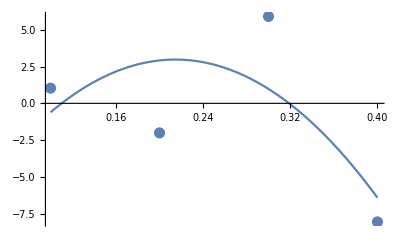

```mathematica
m=2;{P[X],((P[X]-Ft[X])//Chop)==0,δ}
Gr
```

Задание 2;

3

{47.876-796.938 X+3832.4 X^2-5474.17 X^3,True,6.3528×10^-12,True}

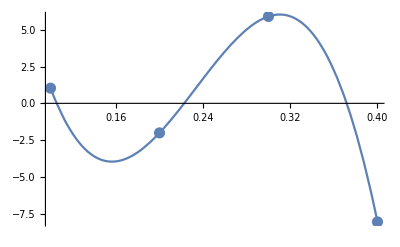

```mathematica
eps=1/2*10^-3;
m=1;While[δ>1/2*10^-3,m=m+1]
m1=m
{P[X],Chop[P[X]-Ft[X],10^-8]==0,δ1=δ, δ1<eps}
Gr
```

```mathematica
m=m-1;
m2=m
{P[X],((P[X]-Ft[X])//Chop)==0,δ2=δ,δ2<eps}
Gr
```

2

{-9.60275+117.247 X-273.225 X^2,True,3.67218,False}

-Graphics-

```mathematica
If[(k1=eps/δ1)<(k2=δ2/eps),opt=m1,opt=m2]
```

2